# Monte Carlo Integration

Jonathan Gorard

For many complex integrals, expression in terms of elementary functions is difficult or impossible. In these situations, Monte Carlo integration, or integration by random sampling, provides a useful estimate for the value of a definite integral. By generating random points and calculating the percentage that fall within the function to be integrated, one can approximate the definite integral.

## Principles and Motivation

The integral of the Gaussian function is famously inexpressible in terms of elementary functions, yet there are many situations (e.g. when computing normalizing constants of distributions in statistics) in which the definite integrals of such functions appear and must be computed numerically.

Plot the Gaussian function on the interval [0,1]:

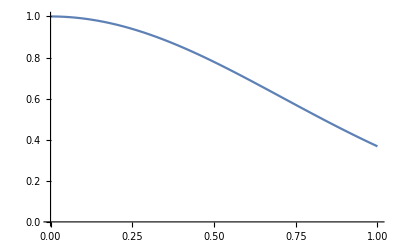

```mathematica
Plot[Exp[-x^2],{x,0,1},PlotRange->{0,1}]
```

When definite integrals cannot be evaluated analytically, one approach to evaluating them numerically (assuming that the range of the integrand is bounded) is to treat the limits of integration and the local maximum and minimum of the function within that region as the edges of a rectangle. Then, one places random points inside that rectangle using uniform sampling.

Add the random points to the Gaussian plot:

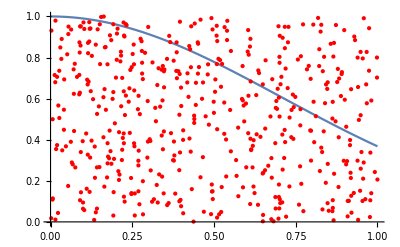

```mathematica
Show[Plot[Exp[-x^2],{x,0,1},PlotRange->{0,1}],Graphics[{Red,Point[RandomPoint[Rectangle[],500]]}]]
```

Clearly, the probability of any such a point being enclosed between the function and the y axis is equal to the ratio of the area enclosed by the function to the total area of the rectangle. Thus, the ratio of the number of points enclosed by the function to the total number of points, when multiplied by the area of the rectangle (which, in this case, is 1), gives an approximation to the value of the definite integral.

## Approximating the Gaussian Integral

A point is enclosed by the function if its y coordinate is less than or equal to the value of the function at its respective x coordinate (since, in this case, the function is strictly non-negative). Conversely, a point is not enclosed by the function if its y coordinate is strictly greater than the value of the function at its respective x coordinate.

Generate a list of points in a unit rectangle:

```mathematica
randomPoints=RandomPoint[Rectangle[],1000];
```

Determine the set of points enclosed by the Gaussian function:

```mathematica
insidePoints=Cases[randomPoints,{x_,y_}/;y≤Exp[-x^2]];
```

Determine the set of points that lie outside the Gaussian function:

```mathematica
outsidePoints=Cases[randomPoints,{x_,y_}/;y>Exp[-x^2]];
```

Show the points enclosed by the Gaussian function in blue and all others in red:

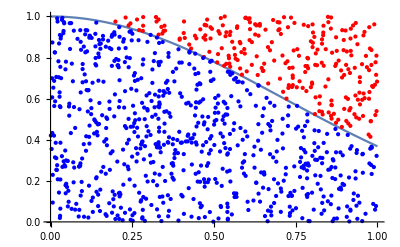

```mathematica
Show[Plot[Exp[-x^2],{x,0,1},PlotRange->{0,1}],Graphics[{Red,Point[outsidePoints]}],Graphics[{Blue,Point[insidePoints]}]]
```

The fraction of the points enclosed by the function provides an approximation of the value of the definite integral. The more points that are placed, the better the approximation.

Approximate the value of the Gaussian integral:

```mathematica
Length[insidePoints]/Length[randomPoints]//N
```

0.744

Compute the error percentage:

```mathematica
PercentForm[1-NIntegrate[Exp[-x^2],{x,0,1}]/%]
```

-0.3796%

This method of uniform sampling is known as naive Monte Carlo integration.

## Higher-Dimensional Generalization

In practice, one-dimensional integrals can be approximated much more efficiently (except in highly pathological cases) by using interpolating functions as quadrature rules. A good example is given by the Newton–Cotes formulas, which approximate a function by interpolating between polynomials placed at equally spaced points. As such, Monte Carlo methods are usually only practical when evaluating integrals in many dimensions, since (unlike interpolation methods) the technique generalizes naturally to spaces of arbitrary dimensionality.

Plot the two-dimensional Gaussian inside a box of volume 1:

```mathematica
Plot3D[Exp[-(x^2+y^2)],{x,0,1},{y,0,1},PlotRange->{0,1}]
```

-Graphics3D-

Now we generalize the Monte Carlo procedure by sampling uniformly inside the space and determining which points are enclosed by the surface.

Pick a set of 10,000 random points to place inside the space:

```mathematica
randomPoints2=RandomPoint[Cuboid[],10000];
```

Determine the set of points enclosed by the Gaussian surface:

```mathematica
insidePoints2=Cases[randomPoints2,{x_,y_,z_}/;z≤Exp[-(x^2+y^2)]];
```

Determine the set of points that lie outside the Gaussian surface:

```mathematica
outsidePoints2=Cases[randomPoints2,{x_,y_,z_}/;z>Exp[-(x^2+y^2)]];
```

Show the points enclosed by the Gaussian surface in blue and all others in red:

```mathematica
Show[Plot3D[Exp[-(x^2+y^2)],{x,0,1},{y,0,1},PlotRange->{0,1}],Graphics3D[{Red,Point[outsidePoints2]}],Graphics3D[{Blue,Point[insidePoints2]}]]
```

-Graphics3D-

Once again, we obtain an asymptotic approximation to the value of the (higher-dimensional) integral.

Approximate the value of the higher-dimensional integral:

```mathematica
Length[insidePoints2]/Length[randomPoints2]//N
```

0.5635

Compare with Mathematica’s approximation:

```mathematica
PercentForm[1-NIntegrate[Exp[-(x^2+y^2)],{x,0,1},{y,0,1}]/%]
```

1.021%

Many improvements can be made to the uniform sampling approach used in naive Monte Carlo integration. For instance, the target area may be split into several subdomains that are each sampled separately (known as stratified sampling), a nonuniform sampling distribution may be used (known as importance sampling) and so on. When employed correctly, such approaches can dramatically reduce the standard error of the approximation by increasing its convergence time. Finding improved estimates for the error in Monte Carlo techniques remains an active area of research.